## Cеминар 2

```mathematica
ss[x_] := -x Log[x] - (1-x)Log[1-x];
```

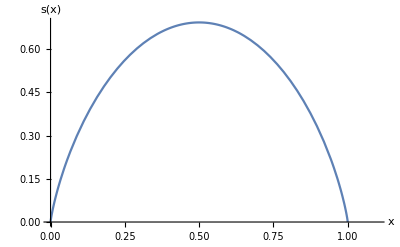

```mathematica
sotx = Plot[ss[x], {x, 0, 1.1}, GridLines->{{{1/2,Red}},None}, GridLinesStyle->Directive[Dashed, Thick], 
AxesLabel->{x, s[x]}]
```

```mathematica
Export[NotebookDirectory[]<>"img\\sem2im1.pdf",sotx];
```

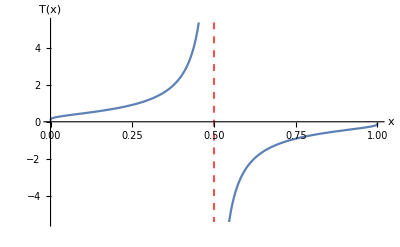

```mathematica
Totx = Plot[1/Log[(1-x)/x], {x,0,1}, ExclusionsStyle->{{Red, Dashed, Thick}},
GridLinesStyle->Directive[Dashed, Thick], 
AxesLabel->{x, T[x]}]
```

```mathematica
Export[NotebookDirectory[]<>"img\\sem2im2.pdf",Totx];
```

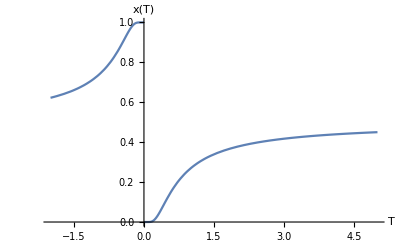

```mathematica
xotT = Plot[1/(1 + Exp[1/T]), {T, -2, 5}, GridLines->{None,{{1/2,Red}}}, GridLinesStyle->Directive[Dashed, Thick], 
AxesLabel->{T, x[T]}]
```

```mathematica
Export[NotebookDirectory[]<>"img\\sem2im3.pdf",xotT];
```

General::munfl: 4.89021×10^7 9.4547712561×10^-3038 is too small to represent as a normalized machine number; precision may be lost.

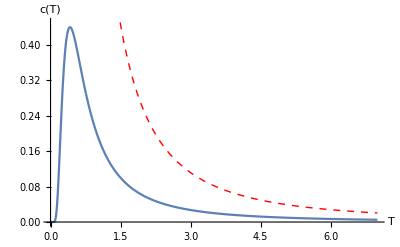

```mathematica
cotT = Plot[{1/T^2 Exp[1/T]/(1 + Exp[1/T])^2, 1/T^2}, {T, 0, 7}, PlotStyle->{Automatic, {Red, Dashed, Thick}}, PlotRange->{0, 0.45}, AxesLabel->{T, c[T]}]
```

```mathematica
Export[NotebookDirectory[]<>"img\\sem2im4.pdf",cotT];
```

## Cеминар 4

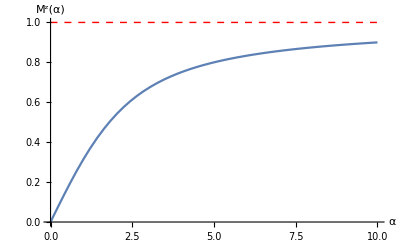

```mathematica
Mzotalpha = Plot[{Coth[a] - 1/a, 1}, {a, 0, 10},PlotStyle->{Automatic,{Red,Dashed,Thick}},AxesLabel->{α,(M^z)[α]}]
```

```mathematica
Export[NotebookDirectory[]<>"img\\sem4im1.pdf",Mzotalpha];
```

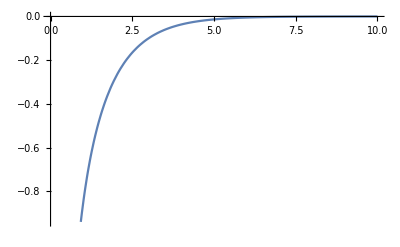

```mathematica
qMzotalpha = Plot[Coth[a] - Coth[a/2], {a, 0, 10}]
```

## Семинар 5

```mathematica
muotT = Plot[{- T Log[T^(3/2)]}, {T, 0, 2},AxesLabel->{T,μ[T, V, N]}, PlotRange->Full]
```

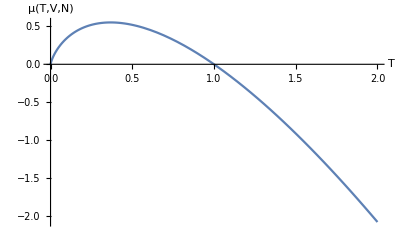

```mathematica
Export[NotebookDirectory[]<>"img\\sem5im1.pdf",muotT];
```

## Семинар 6

General::munfl: Exp[-12237.8] is too small to represent as a normalized machine number; precision may be lost.

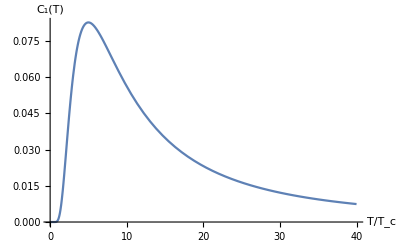

```mathematica
C1orto = Plot[{(√(700/3))/T^2 Exp[-10/T]}, {T, 0, 40},AxesLabel->{T/Subscript[T, c],Subscript[C, 1][T]}, PlotRange->Full]
```

```mathematica
Export[NotebookDirectory[]<>"img\\sem6im1.pdf",C1orto];
```

## Семинар 7

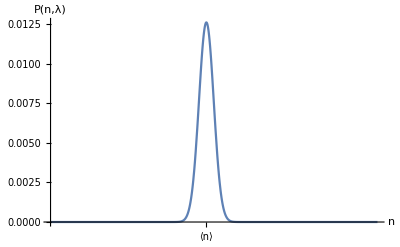

```mathematica
l = 1000;
gauss = Plot[1/(√(2 π l))Exp[(- (n-l)^2)/(2l)], {n, l /3, √3 l}, PlotRange->All,AxesLabel->{n,P[n, λ], λ>>1}, Ticks-> {{{1000, "⟨n⟩"}},{}}]
```

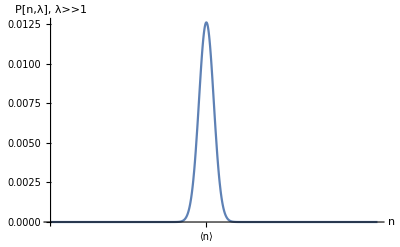

```mathematica
gausss =Show[gauss,AxesLabel->{HoldForm[n],RawBoxes[RowBox[{RowBox[{"P","[",RowBox[{TagBox["n",HoldForm],",","λ"}],"]"}],","," ",RowBox[{"λ",">>","1"}]}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

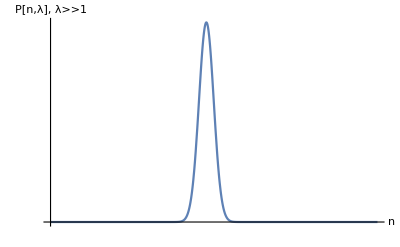

```mathematica
gausss = Show[%41,Ticks->None,Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

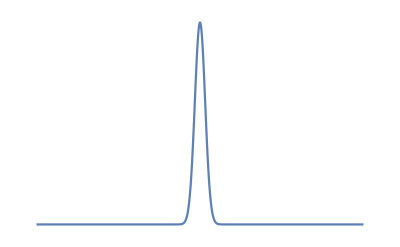

```mathematica
Show[gauss,Axes->False]
```

```mathematica
Export[NotebookDirectory[]<>"img\\sem7im1.pdf",gausss];
```

## Семинар 9

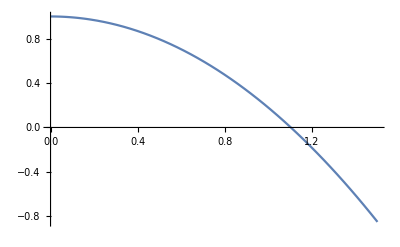

```mathematica
mu8otT= Plot[1 - π^2/12(T)^2, {T,0,1.5}]
```

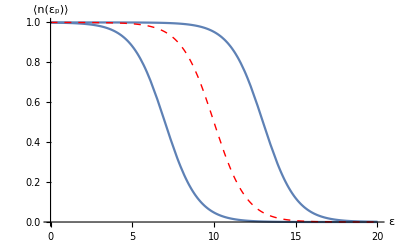

```mathematica
notEpsPM = Plot[{{1/(Exp[e - 3 - 10]+1),1/(Exp[e + 3 - 10]+1)}+0,1/(Exp[e  - 10]+1) }, {e, 0, 20}, PlotStyle->{Automatic,{Red,Dashed,Thick}},AxesLabel->{ε,⟨n[Subscript[ε, p]]⟩}, Ticks -> None]
```

```mathematica
Export[NotebookDirectory[]<>"img\\sem9im2.pdf",notEpsPM];
```

```mathematica
ExpandFileName["C:\\Users\\Евгений\\Desktop\\github_repos\\notes_7sem\\statphys\\belemuk\\img\\sem9im2.pdf"]
```

C:\Users\Евгений\Desktop\github_repos\notes_7sem\statphys\belemuk\img\sem9im2.pdf

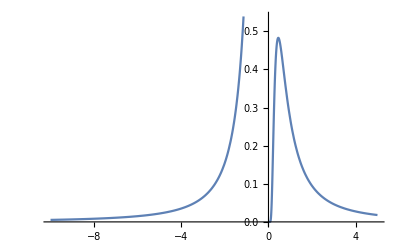

```mathematica
Plot[1/x^2 1/(1+Exp[1/x]), {x, -10, 5}]
```

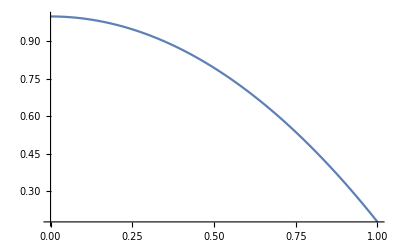

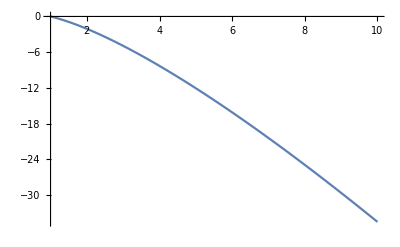

```mathematica
Plot[1 - π^2/12 T^2, {T, 0, 1}]
Plot[- T Log[(T)^(3/2)], {T, 1, 10}]
```

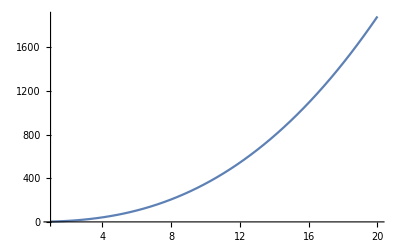

```mathematica
Plot[T^(5/2)Exp[1/T], {T,1, 20}]
```

```mathematica
Series[T^(5/2)Exp[1/T], {T, ∞, 1}]
```

T^(5/2)+T^(3/2)+(√T)/2+(√(1/T))/6+O[1/T]^(3/2)